## Quasinormal modes

We want to have a look at the quasinormal modes of an AdS black hole in 3+1 dimensions. The metric of this black hole is given by

	ds^2 = -f(r) dt^2 + (f(r))^-1 dr^2 + r^2  (dθ^2 + sin^2 θ dϕ^2)
with 
	f(r) = r^2/R^2+ 1 - r_0/r
	
where R is the AdS radius, set to 1 in this notebook, and r_0 is a constant related to the mass of the black hole.
In this background geometry, we want to look at the solutions of the scalar massless wave equation 

	∇_a ∇^a Φ = 0

### Quasinormal mode frequency

Near the horizon, we want the solutions to behave as e^(-ⅈω (t+r_*)), so it is convenient to switch to ingoing Eddington Frinkelstein coordinates. Defining the lightray coordinate as v = t + r_* with r_* = ∫dr/(f(r)) the tortoise coordinate, we get 

	ds^2 = -f(r) dv^2 + 2 dv dr + r^2  (dθ^2 + sin^2 θ dϕ^2)

```mathematica
coord = {v, r, θ, ϕ};
metric = {{-f[r], 1, 0, 0}, {1, 0, 0 , 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[θ]^2}};
$Assumptions = And[v∈Reals, r∈Reals, θ∈Reals, ϕ∈Reals];
SetDirectory["/home/silke/Documents/Wolfram Mathematica"]
<< diffgeo.m
```

/home/silke/Documents/Wolfram Mathematica

```mathematica
metric // MatrixForm
```

(-f[r] | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

We are interested in the lowest mode spherically symmetric solutions, and can make an ansatz for the solution

```mathematica
Φ[v, r] = 1/r ψ[r] Exp[-ⅈ ω v];
```

which leads to a radial equation for ψ.

```mathematica
gradient = partial[Φ[v, r]].inverse;
pde = divergence[gradient] == 0 //Simplify
```

(-2 ⅈ ω+f'[r]) ψ'[r]+f[r] ψ''[r]==(ψ[r] f'[r])/r

So we get as equation

	f(r) d^2/dr^2 ψ(r)  +  (-2 ⅈ ω + f'(r))  d/dr ψ(r) - (f'(r))/r ψ(r) = 0
	
consistent with the general radial wave equation with V(r) = (f'(r))/r.

In order for the coordinate interval to be finite, we change to the coordinate x = 1/r, and using

	d/dr = dx/dr d/dx = -1/r^2 d/dx =  -x^2 d/dx
	
we get

	f(r) d^2/dr^2 ψ(r)  +  (-2 ⅈ ω + f'(r))  d/dr ψ(r) - (f'(r))/r ψ(r) = 0

f(r) x^2 d/dx(x^2 d/dx ψ(x))  -  (-2 ⅈ ω + f'(r))  x^2 d/dx ψ(r) - (f'(r))/r ψ(r) = 0

 f(r) x^4 d^2/dx^2 ψ(x) + (2 ⅈ ω x^2 - f'(r)x^2 + 2f(r)  x^3 )d/dx ψ(x) -  x f'(r)ψ(x) = 0
	
Now rewriting the function f(r):

	f(r) = r^2+ 1 - r_0/r  = 1/x^2+ 1 - r_0 x
f'(r) = 2r + r_0/r^2 = 2/x + r_0 x^2

2f(r) x^3 = 2x+ 2 x^3 - 2 r_0 x^4
f(r) x^4 = x^2+ x^4 - r_0 x^5
f'(x) x = 2 + r_0 x^3
-f'(x) x^2 = -2x - r_0 x^4 
	
So this gives

	f(r) x^4 d^2/dx^2 ψ(x) + (2 ⅈ ω x^2 - f'(r)x^2 + 2f(r)  x^3 )d/dx ψ(x) -  x f'(r)ψ(x) = 0

(x^2+ x^4 - r_0 x^5)d^2/dx^2 ψ(x) + (2 ⅈ ω x^2 - 2x - r_0 x^4 + 2x+ 2 x^3 - 2 r_0 x^4)d/dx ψ(x) -  (2 + r_0 x^3)ψ(x) = 0

(- r_0 x^5+ x^4+ x^2 )d^2/dx^2 ψ(x) + ( -3 r_0 x^4 + 2 x^3 + 2 ⅈ ω x^2)d/dx ψ(x) +  (- r_0 x^3 - 2)ψ(x) = 0

(+ r_0 x^5- x^4- x^2)/(x - xh)d^2/dx^2 ψ(x) + (3 r_0 x^4 - 2 x^3 - 2 ⅈ ω x^2)/(x - xh)d/dx ψ(x) +  ( r_0 x^3 + 2)/(x - xh)ψ(x) = 0         if x ≠ xh, where x_+ is the horizon radius satisfying r_0 = (xh^2 + 1)/xh^3

So we get

	s(x)d^2/dx^2 ψ(x) + (t(x))/(x - xh)d/dx ψ(x) +  (u(x))/(x - xh)^2 ψ(x) = 0         if x ≠ xh

	with
		s(x) =(r_0 x^5- x^4- x^2)/(x - xh)       (3.2)
		t(x) = 3 r_0 x^4 - 2 x^3 - 2 ⅈ ω x^2       (3.3)
		u(x) = (r_0 x^3 + 2)(x - xh) = f'(x) x (x - xh) = V(x) (x - xh)       (3.4)

```mathematica
s[x_, xh_]:=((1/xh^3 + 1/xh)x^5-x^4-x^2)/(x-xh);
t[x_, xh_, ω_]:=3 (1/xh^3 + 1/xh) x^4-2 x^3-2 x^2 ⅈ ω;
V[x_, xh_]:= 2 + (1/xh^3 + 1/xh) x^3;
u[x_, xh_]:=(x-xh)V[x, xh];
```

We can expand these functions around the horizon, since they are polynomials of degree 4:

	s(x) = ∑_(n=0)^d s_n (x - xh)^n
t(x) = ∑_(n=0)^d t_n (x - xh)^n
u(x) = ∑_(n=0)^d u_n (x - xh)^n

```mathematica
coefs[n_, xh_]:=SeriesCoefficient[Series[s[x, xh],{x,xh,n}],n];coefu[n_, xh_]:=SeriesCoefficient[Series[u[x, xh],{x,xh,n}],n];coeft[n_, xh_]:=SeriesCoefficient[Series[t[x, xh,ω],{x,xh,n}],n];
```

We also expand ψ(x) around the horizon:

	ψ(x) = ∑_(n=0)^∞ a_n (x - xh)^n
	
Substituting this in the equation we had before, we get:

	s(x) d^2/dx^2 ψ(x) + (t(x))/(x - xh) d/dx ψ(x) + (u(x))/(x - xh)^2 ψ(x) = 0
∑_m ∑_k [s_m (x - xh)^m a_k k(k-1) (x - xh)^(k-2) + t_m (x - xh)^m a_k k (x - xh)^(k-2) + u_m (x - xh)^m a_k (x - xh)^(k-2)] = 0
∑_m ∑_k [s_m a_k k(k-1) (x - xh)^(m+k-2) + t_m a_k k (x - xh)^(m+k-2) + u_m a_k (x - xh)^(m+k-2)] = 0

Substitute n = m +k, so we get 

	∑_n ∑_k [s_(n-k)a_k k(k-1) + t_(n-k) a_k k + u_(n-k) a_k] (x - xh)^(n-2)= 0
	
Since all terms in n are linear independent, and s_(n-k) = t_(n-k)=u_(n-k) = 0 for k > n, we get
	
	∑_(k=0)^n [s_(n-k)a_k k(k-1) + t_(n-k) a_k k + u_(n-k) a_k]= 0
∑_(k=0)^(n-1) [s_(n-k)k(k-1) + t_(n-k) k + u_(n-k)] a_k + [s_0 n(n-1) + t_0 n + u_0]a_n = 0
a_n =-1/(s_0 n(n-1) + t_0 n + u_0) ∑_(k=0)^(n-1) [s_(n-k)a_k k(k-1) + t_(n-k) a_k k + u_(n-k) a_k]
	
So this results in a recursion relation:
 	
 	a_n =-1/P_n∑_(k=0)^(n-1) [k(k-1) s_(n-k) + k t_(n-k) + u_(n-k)] a_k 
 	
 with (using u_0= 0) 
 
 	P_n = n(n-1) s_0 + n t_0
 
 We can set a_0 = 1 without loss of generality due to linearity.

```mathematica
P[n_, xh_, ω_]:=n*(n-1)*coefs[0, xh]+n*coeft[0, xh];
```

```mathematica
a[0, xh_]=1;
a[n_, xh_]:=a[n, xh]=Simplify[-1/P[n,xh, ω] Sum[(j(j-1)coefs[n-j, xh] + j coeft[n-j, xh]+coefu[n-j, xh])a[j, xh],{j,0,n-1}]];
```

We now have an expression for ψ(x), from which we want to determine ω. In order for ψ to be a quasinormal mode, we require that ψ(r->+∞) -> 0 or thus ψ(x -> 0) -> 0. This determines a constraint on ω:

	ψ(x->0) = ∑_(n=0)^∞ a_n (- xh)^n -> 0

```mathematica
asum[0, xh_] = a[0, xh];
asum[NN_, xh_] := asum[NN, xh] = asum[NN-1, xh] + a[NN, xh]*(-xh)^NN;
```

To make an estimate of the values of ω, we plot this sum in the complex plane. Let us assume a large black hole with radius 100 to explain the principle.

```mathematica
rhtest  = 100;
xhtest = 1/rhtest;
```

```mathematica
ComplexPlot[asum[45,xhtest], {ω, -1500ⅈ, 1500}, AxesLabel->{"Re[ω]", "Im[ω]"}]
```

-Graphics-

We estimate the value for the first order quasinormal mode as ω = 180-270I and use this estimate to determine the exact solution.

```mathematica
ωsol[NN_,xh_, ωguess_]:=FindRoot[asum[IntegerPart[NN], xh]==0,{ω,ωguess}][[1]][[2]];
```

Since we cannot calculate this sum with infinitely many terms, the convergence of the series is important. One can plot the dependence of the solution on the number of terms in the sum,

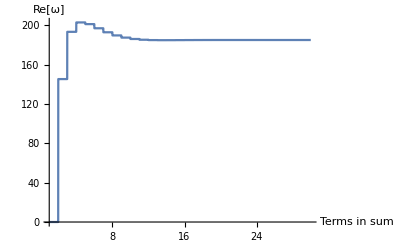

```mathematica
Plot[Re[ωsol[NN, xhtest, 180-270I]], {NN, 1, 30}, PlotRange -> All, AxesLabel->{"Terms in sum", "Re[ω]"}]
```

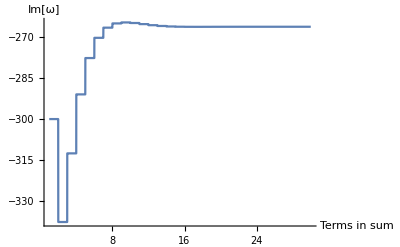

```mathematica
Plot[Im[ωsol[NN, xhtest, 180-270I]], {NN, 1, 30}, PlotRange -> All, AxesLabel->{"Terms in sum", "Im[ω]"}]
```

, and conclude that the result for ω converges for a finite number of terms in the sum. We can thus approximate the frequency ω of the lowest quasinormal mode as

```mathematica
ωval = ωsol[40,xhtest, 180-270I]
```

184.953-266.386 ⅈ

### Lowest quasinormal mode

Let us now have a look at the quasinormal mode itself. As a reminder: 

	Φ(v, r) = 1/r ψ(r) e^(-ⅈ ω v)
	
with 

	ψ(x) = ∑_(n=0)^∞ (a_n(x - xh))^n

```mathematica
Psi[x_,xh_,Nit_]:=Sum[a[i, xh]*(x-xh)^(i),{i,0,Nit}] ;
```

This sum has to be convergent for 0<x<xh (=0.01), so we plot again the dependence of the result on the number of terms in the sum.

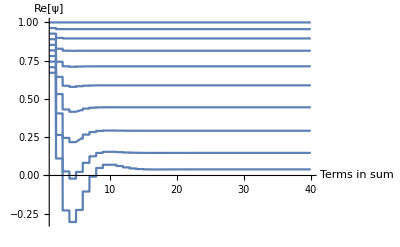

```mathematica
Plot[Table[Re[Psi[x,xhtest,NN]/. ω -> ωval], {x, 0.001, 0.01, 0.001}],{NN, 1, 40 }, PlotRange->All, AxesLabel->{"Terms in sum", "Re[ψ]"}]
```

Since we see that this sum converges quite fast, we can take 20 terms to plot the surface.

```mathematica
QNM[v_, r_, rh_, NN_] := 1/r Psi[1/r,1/rh,NN] Exp[-ⅈ ω v]
```

```mathematica
Plot3D[Re[QNM[v, r, rhtest, 20]/.ω->ωval], {v, 0, 0.05}, {r, rhtest, 1000}, AxesLabel-> {v, r, Φ}, PlotRange->{{0, 0.05}, {rhtest, 1000}, {-0.0003, 0.001}}, BoxRatios->{1, 1, 0.7}]
```

-Graphics3D-

In this plot, you can clearly see the ringdown and thermalisation of the field.

### Higher modes

We can repeat the same procedure, but using another guess for the quasinormal frequency, to determine the higher order modes.

```mathematica
ωvals = {ωsol[40, xhtest, 180-270I], ωsol[40, xhtest,  300-500I], ωsol[40, xhtest, 450-700I],  ωsol[40, xhtest, 570-930I], ωsol[40, xhtest, 700-1200I]};
ωval = ωvals[[1]];
Plot3D[Re[QNM[v, r, rhtest, 20]/.ω->ωval], {v, 0, 0.05}, {r, rhtest, 1000}, AxesLabel-> {v, r, Φ}, PlotRange->{{0, 0.05}, {rhtest, 1000}, {-0.0003, 0.001}}, BoxRatios->{1, 1, 0.7},  PlotLabel->"ω = "  ~~ToString[ωval]]
ωval = ωvals[[2]];
Plot3D[Re[QNM[v, r, rhtest, 20]/.ω->ωval], {v, 0, 0.05}, {r, rhtest, 1000}, AxesLabel-> {v, r, Φ}, PlotRange->{{0, 0.05}, {rhtest, 1000}, {-0.0003, 0.001}}, BoxRatios->{1, 1, 0.7},  PlotLabel->"ω = "  ~~ToString[ωval]]
ωval = ωvals[[3]];
Plot3D[Re[QNM[v, r, rhtest, 20]/.ω->ωval], {v, 0, 0.05}, {r, rhtest, 1000}, AxesLabel-> {v, r, Φ}, PlotRange->{{0, 0.05}, {rhtest, 1000}, {-0.0003, 0.001}}, BoxRatios->{1, 1, 0.7}, PlotLabel->"ω = "  ~~ToString[ωval]]
ωval = ωvals[[4]];
Plot3D[Re[QNM[v, r, rhtest, 20]/.ω->ωval], {v, 0, 0.05}, {r, rhtest, 1000}, AxesLabel-> {v, r, Φ}, PlotRange->{{0, 0.05}, {rhtest, 1000}, {-0.0003, 0.001}}, BoxRatios->{1, 1, 0.7},  PlotLabel->"ω = "  ~~ToString[ωval]]
ωval = ωvals[[5]];
Plot3D[Re[QNM[v, r, rhtest, 30]/.ω->ωval], {v, 0, 0.05}, {r, rhtest, 1000}, AxesLabel-> {v, r, Φ}, PlotRange->{{0, 0.05}, {rhtest, 1000}, {-0.0003, 0.001}}, BoxRatios->{1, 1, 0.7}, PlotLabel->"ω = "  ~~ToString[ωval]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

### Influence of the temperature

To have a look at the influence of the temperature, we use the relation between temperature and horizon radius. The Hawking temperature can be calculated as follows:

Around the horizon radius and neglecting the angular parts, we can write

	ds^2 = f(r) dτ^2 + 1/(f(r)) dr^2
         = (f(rh) + f'(rh)(r-rh)) dτ^2 + 1/(f(rh) + f'(rh)(r-rh)) dr^2
        = f'(rh)(r-rh) dτ^2 + 1/(f'(rh)(r-rh)) dr^2
	
and using u=r-rh

	ds^2 = f'(rh)u dτ^2 + 1/(f'(rh) u) du^2

As a function of a new variable w, defined as

	1/(f'(rh) u) du^2 = dw^2 -> dw = 1/(√(f'(rh) u)) du -> w = (2 √u)/(√(f'(rh)))

this metric can be rewritten as

	ds^2 = (f'(rh)^2)/4 w^2 dτ^2 + dw^2
          = w^2 (d((f'(rh))/2 τ))^2 + dw^2

Comparing this metric with the polar metric

	ds^2 = dr^2+r^2 dθ^2 
	
we see that these metrics are equivalent upon defining r = w and θ = (f'(rh))/2 τ. In order to avoid a conical singularity for periodicity τ = β, the periodicity β in τ should correspond to a rotation by 2π in θ. 

	(f'(rh))/2 β = 2π -> β = (4π)/(f'(rh)) -> T = (f'(rh))/(4π)

So we get 

	T=(3 rh^2 + R^2)/(4π rh R^2)
	
And for large black holes rh >> R
	
	T=(3rh)/(4π R^2)

```mathematica
T[rh_] := (3 rh^2 + 1)/(4π rh);
```

In order to determine the frequencies, the estimates of the frequencies can again be determined from complex plots.

We first make a plot of the frequency as a function of the radius of the black hole. This can be seen to be be linear over the whole range of radii, from intermediate to large black holes.

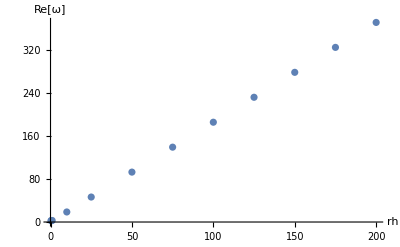

```mathematica
ListPlot[{{1/3,Re[ωsol[10,3,2-I]]}, {1/2,Re[ωsol[10,2,1-2I]]}, {1,Re[ωsol[10,1,2-2I]]}, {10,Re[ωsol[10,1/10,20-25I]]}, {25,Re[ωsol[10,1/25,45 - 65I]]}, {50, Re[ωsol[10,1/50,90 - 130 I]]}, {75, Re[ωsol[10,1/75,135 - 200 I]]}, {100, Re[ωsol[10,1/100,185 - 265 I]]}, {125, Re[ωsol[10,1/125,230 - 330 I]]}, {150,Re[ωsol[10,1/150,270 - 400 I]]}, {175,  Re[ωsol[10,1/175,320 - 470 I]]}, {200, Re[ωsol[10,1/200, 370 - 530 I]]}}, AxesLabel-> {"rh", "Re[ω]"}]
```

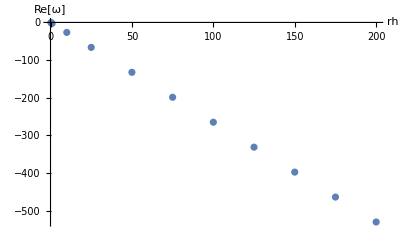

```mathematica
ListPlot[{{1/3, Im[ωsol[10,3,2-I]]}, {1/2,Im[ωsol[10,2,1-2I]]}, {1,Im[ωsol[10,1,2-2I]]}, {10,Im[ωsol[10,1/10,20-25I]]}, {25,Im[ωsol[10,1/25,45 - 65I]]}, {50, Im[ωsol[10,1/50,90 - 130 I]]}, {75, Im[ωsol[10,1/75,135 - 200 I]]}, {100, Im[ωsol[10,1/100,185 - 265 I]]}, {125, Im[ωsol[10,1/125,230 - 330 I]]}, {150,Im[ωsol[10,1/150,270 - 400 I]]}, {175,  Im[ωsol[10,1/175,320 - 470 I]]}, {200, Im[ωsol[10,1/200, 370 - 530 I]]}}, AxesLabel-> {"rh", "Re[ω]"}]
```

Since for large black holes, the temperature scales linearly with the black hole radius, one could expect the frequency to be linear in the temperature. For large black holes, this is indeed the case.

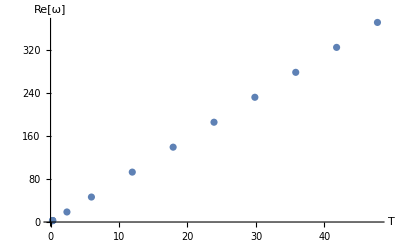

```mathematica
ListPlot[{{T[1/3],Re[ωsol[10,3,2-I]]}, {T[1/2],Re[ωsol[10,2,1-2I]]}, {T[1],Re[ωsol[10,1,2-2I]]}, {T[10],Re[ωsol[10,1/10,20-25I]]},{T[25],Re[ωsol[10,1/25,45 - 65I]]}, {T[50], Re[ωsol[10,1/50,90 - 130 I]]}, {T[75], Re[ωsol[10,1/75,135 - 200 I]]}, {T[100], Re[ωsol[10,1/100,185 - 265 I]]}, {T[125], Re[ωsol[10,1/125,230 - 330 I]]}, {T[150],Re[ωsol[10,1/150,270 - 400 I]]}, {T[175],  Re[ωsol[10,1/175,320 - 470 I]]}, {T[200], Re[ωsol[10,1/200, 370 - 530 I]]}}, AxesLabel-> {"T", "Re[ω]"}]
```

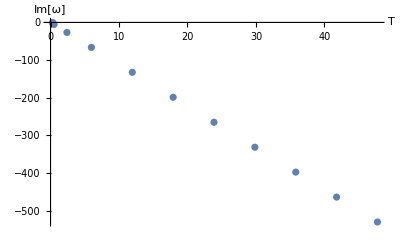

```mathematica
ListPlot[{{T[1/3],Im[ωsol[10,3,2-I]]}, {T[1/2],Im[ωsol[10,2,1-2I]]}, {T[1],Im[ωsol[10,1,2-2I]]}, {T[2],Im[ωsol[10,1/2,4-5I]]}, {T[10],Im[ωsol[10,1/10,20-25I]]}, {T[25],Im[ωsol[10,1/25,45 - 65I]]}, {T[50], Im[ωsol[10,1/50,90 - 130 I]]}, {T[75], Im[ωsol[10,1/75,135 - 200 I]]}, {T[100], Im[ωsol[10,1/100,185 - 265 I]]}, {T[125], Im[ωsol[10,1/125,230 - 330 I]]}, {T[150],Im[ωsol[10,1/150,270 - 400 I]]}, {T[175],  Im[ωsol[10,1/175,320 - 470 I]]}, {T[200], Im[ωsol[10,1/200, 370 - 530 I]]}}, AxesLabel-> {"T", "Im[ω]"}]
```

The linear relation between the radius and temperature breaks down for intermediate black holes. When plotting the frequency as a function of the black hole radius for intermediate black holes, together with a rescaled temperature as a function of the radius, one can clearly see that the frequency of the black hole no longer follows the temperature for intermediate black holes, but keeps scaling linearly with the radius.

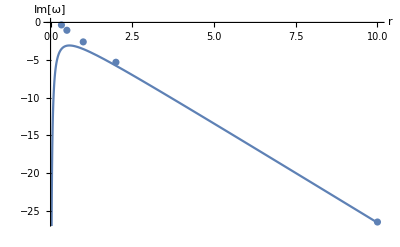

```mathematica
plot1 = ListPlot[{{1/3,Im[ωsol[10,3,2-I]]}, {1/2,Im[ωsol[10,2,1-2I]]}, {1,Im[ωsol[10,1,2-2I]]}, {2,Im[ωsol[10,1/2,4-5I]]}, {10,Im[ωsol[10,1/10,20-25I]]}}, AxesLabel-> {"r", "Im[ω]"}];
plot2 = Plot[T[r] Im[ωsol[10,1/200, 370 - 530 I]]/T[200], {r, 0, 10}];
Show[plot1, plot2]
```

The exact interpretation of this result in the view of AdS/CFT is unclear, since it is not clear how to interpret the black hole radius in the CFT. It would be unexpected from the CFT perspective to observe a deviation from the relation between damping time and temperature. It might be true that the holographic description in terms of the dual Black Holes breaks down beyond some small temperatures.

A more extended discussion of this notebook can be found in our paper.